Зад. 1 Пресметнете:

a) (x+y)^(1/3)+ (x-y)^(1/3) за x=5.1 и y=3.14;
б) √(x/(x+y)+y/(x-y)) при x=1.1 и y=3.14.

```mathematica
(x+y)^(1/3)+(x-y)^(1/3)/.{x->5.1,y->3.14}
√(x/(x+y)+y/(x-y))/.{x->1.1,y->3.14}
```

3.27127

0.+1.13127 ⅈ

Зад. 2 Пресметнете точно, а след това и числено стойността на следните изрази:

a)  [23^3-3(117-48)^2]/(√(7^5-5^7));    б) cos (319π)/12;    в) (83!)/(111!);    г) ln 2981 ;

```mathematica
{(23^3-3(117-48)^2)/(√(7^5-5^7)),N[(23^3-3(117-48)^2)/(√(7^5-5^7))]}
{Cos[(319 π)/12],N[Cos[(319 π)/12]]}
{(83!)/(111!),N[(83!)/(111!)]}
{Log[2981],N[Log[2981]]}
```

{46 ⅈ √(46/1333),0.+8.54519 ⅈ}

{-(-1+√3)/(2 √2),-0.258819}

{1/44682342944049099854590179054637611312231339786240000000,2.23802×10^-56}

{Log[2981],8.00001}

Зад. 3 Да се пресметне втората прозиводна на функцията f(x) = arctg(√(1+x)-√(1-x)) и да се начертае графиката на тази производна в интервала [0,1].

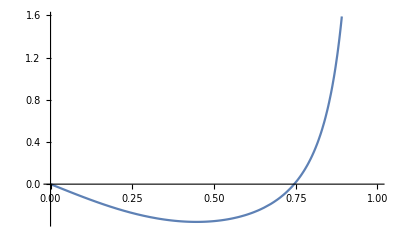

```mathematica
Plot[D[ArcTan[√(1+x)-√(1-x)],{x,2}]/.x->xx,{xx,0,1}]
```

Зад. 4 Дадени са данни за изменението на нивото на въглеродния диоксид в атмосферата. На база на тези данни да се намери функция,  която описва процесът. За целта да се използва вградената фукнция Fit. Графиката на получената функция да се начертае на една графика с данните.

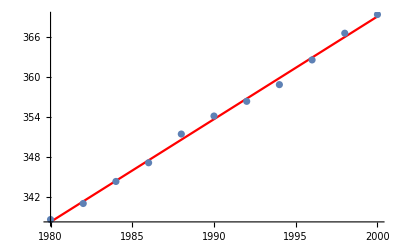

```mathematica
data1={{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
myLeastSquares[x_]=Fit[data1,{1,x},x];
Show[Plot[myLeastSquares[x],{x,1980,2000},PlotStyle->Red],ListPlot[data1]]
```

Зад. 5 Да се напише функция, която намира корените на квадратно уравнение. Функцията да приема като параметри 3 реални числа - коефициентите на квадратния тричлен и да връща списък с корените.
С помощта на функцията да се намерят корените на уравненението 2 x^2+5x+3=0. Резултатът да се провери графично като се начертаят графиката на квадртаната функция заедно с точките в равнината, отговарящи на получените корени.

{-1.,-1.5}

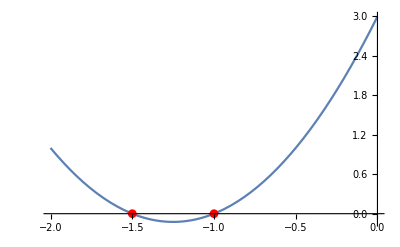

```mathematica
quadRootFinder[a_Real,b_Real,c_Real]:=(
{(-b + √(b^2-4 a c))/(2 a),(-b -√(b^2-4 a c))/(2 a)}
)
quadRootFinder[2.,5.,3.]
Show[Plot[2 x^2+5 x +3,{x,-2,0}],ListPlot[Transpose[{quadRootFinder[2.,5.,3.],{0,0}}],PlotMarkers->Automatic,PlotStyle->Red]]
```